```mathematica
AppendTo[$Path,"~/projects/KnotTheory/trunk/"];
```

```mathematica
<<KnotTheory`
```

Loading KnotTheory` version of January 20, 2015, 10:42:19.1122.
Read more at http://katlas.org/wiki/KnotTheory.

```mathematica
Difference[X_List,Y_List]:=Complement[X,Y]~Join~Complement[Y,X]
```

```mathematica
FirstNonEmpty[f_,L_List]:=Module[{i=1,r},
While[i≤Length[L]∧Length[r=f[L⟦i⟧]]==0,i++];
If[i≤Length[L],r,{}]
]
```

```mathematica
WidthAtMostWitness[k_][K:(_Link|_Knot)]:=WidthAtMostWitness[k][K]=WidthAtMostWitness[k][PD[K]]
WidthAtMostWitness[k_][pd_PD]:=PD@@#⟦1⟧&/@WidthAtMostWitness[k][{},List@@pd]
WidthAtMostWitness[k_][boundary_List,crossings_List]:=
Module[{},
FirstNonEmpty[
Module[{r},
r=WidthAtMostWitness[k][Difference[boundary,(List@@#)],DeleteCases[crossings,#]];
Function[{m},{Append[m⟦1⟧,#],m⟦2⟧}]/@r
]&,Cases[crossings,x_/;Length[Intersection[boundary,List@@x]]≥1/2(Length[boundary]+Length[x]-k)]]
]

WidthAtMostWitness[k_][boundary_List,{}]:={{{},True}}
```

```mathematica
Clear[WidthAtMostQ]
```

```mathematica
WidthAtMostQ[k_][X_]:=Length[WidthAtMostWitness[k][PD[X]]]>0
```

```mathematica
Width[pd_PD]:=Module[{k=0},
While[!WidthAtMostQ[k][pd],k+=2];
k
]
```

```mathematica
Width[K:(_Knot|_Link|_BR)]:=Width[PD[K]]
```

```mathematica
digonCollapseRules={
X[a_,b_,c_,d_]X[b_,a_,e_,f_]:>X[c,d,e,f],
X[a_,b_,c_,d_]X[f_,b_,a_,e_]:>X[c,d,e,f],
X[a_,b_,c_,d_]X[e_,f_,b_,a_]:>X[c,d,e,f],
X[a_,b_,c_,d_]X[a_,e_,f_,b_]:>X[c,d,e,f],

X[d_,a_,b_,c_]X[f_,b_,a_,e_]:>X[c,d,e,f],
X[d_,a_,b_,c_]X[e_,f_,b_,a_]:>X[c,d,e,f],
X[d_,a_,b_,c_]X[a_,e_,f_,b_]:>X[c,d,e,f],

X[c_,d_,a_,b_]X[e_,f_,b_,a_]:>X[c,d,e,f],
X[c_,d_,a_,b_]X[a_,e_,f_,b_]:>X[c,d,e,f],

X[b_,c_,d_,a_]X[a_,e_,f_,b_]:>X[c,d,e,f]
};
```

```mathematica
timesToPD[X_Times]:=PD@@X
timesToPD[X_]:=PD[X]
```

```mathematica
ConwayWidthAtMostQ[k_][X_]:=Length[WidthAtMostWitness[k][timesToPD[(Times@@PD[X])//.digonCollapseRules]]]>0
```

```mathematica
ConwayWidth[pd_PD]:=Module[{k=0},
While[!ConwayWidthAtMostQ[k][pd],k+=2];
k
]
ConwayWidth[K:(_Knot|_Link|_BR)]:=ConwayWidth[PD[K]]
```

```mathematica
WidthAtMostQ[4][PD[Knot[3,1]]]
```

KnotTheory::loading: Loading precomputed data in "PD4Knots`".

True

```mathematica
WidthAtMostQ[4][PD[Knot[8,16]]]
```

False

```mathematica
WidthAtMostQ[6][PD[Knot[8,16]]]
```

True

```mathematica
WidthAtMostWitness[4][Knot[8,16]]
```

{}

```mathematica
WidthAtMostWitness[6][Knot[11,Alternating,43]]
```

{PD[X[10,22,11,21],X[16,12,17,11],X[12,18,13,17],X[18,16,19,15],X[22,20,1,19],X[20,10,21,9],X[6,14,7,13],X[14,6,15,5],X[2,8,3,7],X[8,4,9,3],X[4,2,5,1]]}

KnotTheory::credits: "DrawPD was written by Emily Redelmeier at the University of Toronto in the summers of 2003 and 2004."

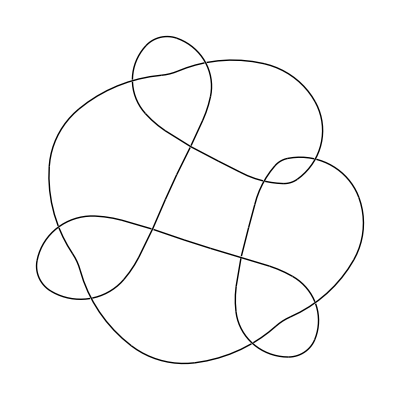

```mathematica
DrawPD/@%
```

```mathematica
Do[Print[{k,Max[Width/@AllKnots[k]]}],{k,3,14}]
```

{3,4}

{4,4}

{5,4}

{6,4}

{7,4}

{8,6}

{9,6}

{10,6}

{11,6}

{12,6}

{13,8}

KnotTheory::loading: Loading precomputed data in "KnotTheory/14N.dts".

{14,8}

```mathematica
Cases[AllKnots[13],K_/;Width[K]==8]
```

{Knot[13,Alternating,1024],Knot[13,Alternating,1698],Knot[13,Alternating,1712],Knot[13,Alternating,3060],Knot[13,Alternating,3781],Knot[13,Alternating,3810],Knot[13,Alternating,3811],Knot[13,Alternating,3812],Knot[13,Alternating,4499],Knot[13,NonAlternating,2018],Knot[13,NonAlternating,2019],Knot[13,NonAlternating,2020],Knot[13,NonAlternating,3659],Knot[13,NonAlternating,3660],Knot[13,NonAlternating,3661],Knot[13,NonAlternating,3662],Knot[13,NonAlternating,3663],Knot[13,NonAlternating,3664],Knot[13,NonAlternating,3665],Knot[13,NonAlternating,3666],Knot[13,NonAlternating,4585],Knot[13,NonAlternating,4586],Knot[13,NonAlternating,4587],Knot[13,NonAlternating,4588],Knot[13,NonAlternating,4589],Knot[13,NonAlternating,4633],Knot[13,NonAlternating,4634],Knot[13,NonAlternating,4635],Knot[13,NonAlternating,4636],Knot[13,NonAlternating,4637],Knot[13,NonAlternating,4638],Knot[13,NonAlternating,4639],Knot[13,NonAlternating,4640],Knot[13,NonAlternating,4641],Knot[13,NonAlternating,4642],Knot[13,NonAlternating,4643],Knot[13,NonAlternating,4644],Knot[13,NonAlternating,4645],Knot[13,NonAlternating,5015],Knot[13,NonAlternating,5016],Knot[13,NonAlternating,5017],Knot[13,NonAlternating,5018],Knot[13,NonAlternating,5019],Knot[13,NonAlternating,5020],Knot[13,NonAlternating,5021],Knot[13,NonAlternating,5022]}

```mathematica
ConwayWidth/@%35
```

{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}

```mathematica
Length[%35]
```

46

```mathematica
Cases[AllKnots[14],K_/;Width[K]≥8]
```

```mathematica
Max[ConwayWidth/@%]
```

6

```mathematica
Length[%%]
```

561

```mathematica
Cases[AllKnots[15],K_/;ConwayWidth[K]≥8];
```

KnotTheory::loading: Loading precomputed data in "KnotTheory/15N.dts".

```mathematica
Length[%]
```

1298

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/scott/projects/exceptional/code

```mathematica
Run["~/bin/plantri -qda -c2 12 > p.out"]
```

0

```mathematica
plantriToPD[S_String]:=Module[{g,edges,edgeNumbering},
g=StringSplit[StringSplit[S," "]⟦2⟧,","];
edges=Map[Sort,Transpose/@Transpose[{Table[{i,i,i,i},{i,1,Length[g]}],(First/@ToCharacterCode/@Characters[#])-96&/@g}],{2}];
edgeNumbering=Union[Cases[edges,{_Integer,_Integer},{2}]];
edgeNumbering=Thread[edgeNumbering->Range[Length[edgeNumbering]]];PD@@(X@@#&/@(edges/.edgeNumbering))
]
```

```mathematica
BasicPolyhedra[n_]:=BasicPolyhedra[n]=Module[{out},
Run["~/bin/plantri -qda -c2 "<>ToString[n+2]<>" > p.out"];
out=ReadString["p.out"];
If[out===EndOfFile,{},
plantriToPD/@StringSplit[out,"\n"]
]
]
```

```mathematica
BasicPolyhedra[6]
```

{PD[X[1,2,3,4],X[1,6,7,5],X[2,5,9,8],X[3,8,11,10],X[4,10,12,6],X[7,12,11,9]]}

```mathematica
Table[Length[BasicPolyhedra[k]],{k,6,16}]
```

{1,0,1,1,3,3,12,19,64,155,510}

```mathematica
Width/@BasicPolyhedra[12]
```

{6,6,6,6,6,8,8,6,6,6,6,6}

```mathematica
DrawPD[BasicPolyhedra[12]⟦6⟧]
```

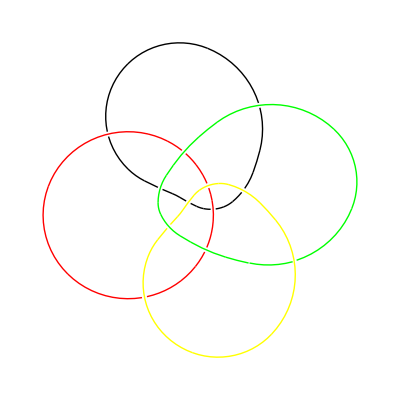

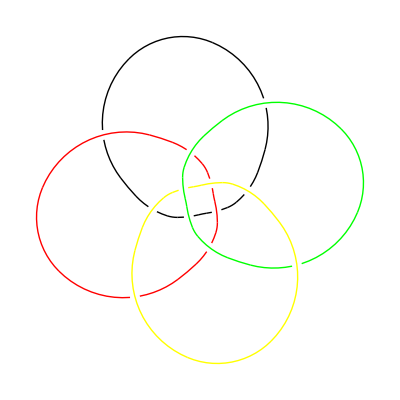

```mathematica
DrawPD[BasicPolyhedra[12]⟦7⟧]
```

```mathematica
Run["~/bin/plantri -qda -c2 14 > p.out"]
```

0

```mathematica
ReadString["p.out"]
```

12 bcde,aefg,ahid,acie,adfb,bejg,bfjk,ckli,chld,flkg,gjlh,hkji
12 bcde,aefg,ahij,ajke,adfb,belg,bflh,cgli,chkj,cikd,djil,fkhg
12 bcde,aefc,abgh,ahij,ajfb,bekg,cfkl,clid,dhlj,dike,fjlg,gkih
12 bcde,afgh,ahid,acij,ajkf,bekg,bfkl,blic,chjd,dile,elgf,gkjh
12 bcde,aefc,abgd,acgh,ahib,bijg,cfkd,dkle,eljf,filk,gjlh,hkji
12 bcde,aefg,aghi,aije,adkb,bklg,bfhc,cgli,chjd,dilk,ejlf,fkjh
12 bcde,aefg,aghd,acij,ajkb,bklg,bfhc,cgli,dhlj,dike,ejlf,fkih
12 bcde,aefg,ahij,ajkl,alfb,belg,bflh,cgki,chkj,cikd,djih,dgfe
12 bcde,aefg,ahid,acij,ajfb,bekg,bfkh,cgli,chld,dlke,fjlg,hkji
12 bcde,aefg,ahij,ajke,adfb,bekg,bfkh,cgli,chlj,cild,dlgf,hkji
12 bcde,aefg,ahid,acij,akfb,bekg,bflh,cgli,chjd,dilk,ejlf,gkjh
12 bcde,aefg,ahid,acij,akfb,bekg,bfkl,clji,chjd,dihl,elgf,gkjh

```mathematica
Width/@BasicPolyhedra[13]
```

{6,6,8,6,6,6,6,6,6,6,6,6,6,8,6,6,6,6,6}

```mathematica
Width/@BasicPolyhedra[14]
```

{6,8,6,6,8,8,8,6,8,6,6,6,8,8,6,8,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,8,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,8,6}

```mathematica
Width/@BasicPolyhedra[15]
```

{6,6,8,6,6,8,8,8,6,8,8,6,6,6,6,8,6,8,6,8,8,8,8,8,8,8,6,6,8,6,6,6,6,8,6,6,6,6,6,6,6,6,6,6,8,8,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,8,6,6,8,6,6,6,6,8,6,8,8,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,8,6,6,6,6,6,6,6,6,8,8,6,8,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,8,6}

```mathematica
Width/@BasicPolyhedra[16]
```

{6,6,6,8,8,6,8,8,8,8,8,6,6,8,6,6,6,6,8,8,6,6,6,8,8,6,8,8,6,6,8,6,6,6,6,6,6,6,8,6,6,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,6,8,6,8,6,8,8,6,8,6,6,6,6,6,6,6,6,8,6,8,8,6,8,8,8,6,8,6,6,8,8,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,8,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,8,8,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,8,8,6,8,6,6,6,6,8,6,8,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,8,8,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,8,6,8,8,8,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,8,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,8,8,8,8,8,8,8,8,6,6,6,6,8,8,8,8,6,8,6,6,6,6,6,6,8,8,6,8,6,8,6,8,6,6,6,6,8,8,8,8,6,8,8,8,8,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,8,8,8,6,8,8,8,8,8,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,8,6,6,6,6,6,6,6,6,6,8,6,6,6,6,6,6,6,6,6,6,6,6,6,6,8,6,8,8,8,6,6,6,6,6,6,6,6,6,6,6,6,6,6,8,8,6,8,6,6,8,8,6,6,6,6,6,8,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,8,8,8,8,6,6,6,6}

```mathematica
Max[Width/@BasicPolyhedra[17]]
```

8

```mathematica
Max[Width/@BasicPolyhedra[18]]
```

8

```mathematica
Max[Width/@BasicPolyhedra[19]]
```

8

```mathematica
Max[Width/@BasicPolyhedra[20]]
```

10